### Normalization

```mathematica
ρ0=1/(4π hR^2 hz)
ρ={R,z}↦ρ0 Exp[-R/hR] Sech[z/hz]^2
```

1/(4 hR^2 hz π)

Function[{R,z},ρ0 Exp[-R/hR] Sech[z/hz]^2]

```mathematica
Integrate[ρ[R,t],{t,-∞,∞},Assumptions->{hz>0}]
```

ⅇ^(-R/hR)/(2 hR^2 π)

```mathematica
2π Integrate[% R,{R,0,∞},Assumptions->{hR>0}]
```

1

### Central surface density

```mathematica
ρ0=.
FullSimplify[Integrate[ρ[R,0],{R,0,∞},Assumptions->{hR>0,hz>0}]]
FullSimplify[Integrate[ρ[0,z],{z,-∞,∞},Assumptions->{hR>0,hz>0}]]
```

hR ρ0

2 hz ρ0

### Random height

```mathematica
ρ0=1/(4π hR^2 hz);
Simplify[ρ[R,z]/Integrate[ρ[R,t],{t,-∞,∞},Assumptions->{hz>0}]]
```

Sech[z/hz]^2/(2 hz)

```mathematica
pz=z↦1/(2hz)Sech[z/hz]^2
```

Function[z,Sech[z/hz]^2/(2 hz)]

```mathematica
Integrate[pz[t],{t,-∞,z},Assumptions->{hz>0}]
```

1/2 (1+Tanh[z/hz])

```mathematica
Pz=z↦1/2+1/2 Tanh[z/hz]
```

Function[z,1/2+1/2 Tanh[z/hz]]

```mathematica
Solve[X==Pz[z],z]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→-hz ArcTanh[1-2 X]}}

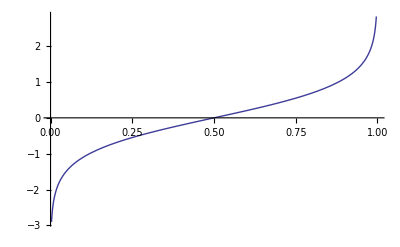

```mathematica
Plot[ArcTanh[2 X-1],{X,0,1}]
```

### Random radius

```mathematica
FullSimplify[(ρ[R,z]R)/Integrate[ρ[R,z]R,{R,0,∞},Assumptions->{z>0,hR>0}]]
```

(ⅇ^(-R/hR) R)/hR^2

```mathematica
pR=R↦(ⅇ^(-R/hR) R)/hR^2
```

Function[R,(ⅇ^(-R/hR) R)/hR^2]

```mathematica
FullSimplify[Integrate[pR[R],R,Assumptions->{hR>0,R>0}]]
```

-(ⅇ^(-R/hR) (hR+R))/hR

```mathematica
Solve[-ⅇ^-u (1+u)==X,u]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{u→-1-ProductLog[X/ⅇ]}}